## functions

```mathematica
DateDifferenceInUnits[date1_DateObject,date2_DateObject,unit_]:=QuantityMagnitude[DateDifference[date1,date2,unit]]
```

```mathematica
PrecedingVal[list_,val_]:=Module[
{nearestVal,nearestPos},
nearestVal=Nearest[list,val][[1]];
nearestPos=Position[list,nearestVal][[1]][[1]];
If[
nearestVal<val,
nearestVal,
list[[nearestPos-1]]
]
]
```

```mathematica
PrecedingPos[list_,val_]:=Module[
{nearestVal,nearestPos},
nearestVal=Nearest[list,val][[1]];
nearestPos=Position[list,nearestVal][[1]][[1]];
If[
nearestVal<val,
nearestPos,
nearestPos-1
]
]
```

```mathematica
SparseTimeMovingAverage[data_List,windowSize_?NumericQ]:=Module[{times,values,averageValues,result,halfWindow,timeWindowIndices},(*Extract times and values*){times,values}=Transpose[data];
(*Half of the window size*)halfWindow=windowSize/2;
(*Moving average calculation*)averageValues=Table[(*Find indices of times within the window around the current time point*)timeWindowIndices=Flatten[Position[times,_?(Abs[#-times[[i]]]<=halfWindow&)]];
If[Length[timeWindowIndices]>0,Mean[values[[timeWindowIndices]]],(*Calculate mean if indices are found*)values[[i]] (*Use current value if no other values are in the window*)],{i,Length[times]}];
(*Combine times with calculated averages*)result=Transpose[{times,averageValues}]]
```

## gas

```mathematica
pulseFactor=0.1;(*one pulse equals this many m3s*)
```

```mathematica
energyContentInGasPerCubicMeter=1000 34/3600;(*kWh*)
```

```mathematica
voltageTimestamps=StringSplit[Import[NotebookDirectory[]<>"gas_pulse_times.txt"],"\n"];
```

```mathematica
startDate=DateObject[voltageTimestamps[[1]]]
```

Wed 22 Nov 2023 17:11:33GMT+1

```mathematica
startDate=DateObject["2023.11.24. 00:00"]
```

Minute: Fri 24 Nov 2023 00:00GMT+1

```mathematica
timeGranularity="Second";
```

```mathematica
voltageTimes=Map[
Round[DateDifferenceInUnits[startDate,DateObject[#],timeGranularity]]
&,voltageTimestamps];
```

```mathematica
Differences[voltageTimes]
```

{5,5,5,5,6,5,5,5,61,266,5,5,5,5,5,5,5,137,32,5,5,6,5,5,5,5,119,92,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,147,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,255,5,5,5,5,5,5,5,45,114,5,5,5,5,5,5,5,110,37,5,5,6,5,5,5,110,27,5,5,5,5,5,5,5,110,185,5,5,70,5,5,5,79,5,5,5,5,94,5,5,5,5,206,54,5,5,5,5,5,132,5,5,5,5,5,6,136,5,5,5,5,5,5,52,229,5,5,5,5,68,6,5,71,5,5,5,86,5,5,5,5,87,5,5,5,5,94,5,5,5,5,99,5,5,5,6,107,5,5,5,5,5,105,5,5,5,5,5,253,75,5,5,5,5,5,5,5,5,354,5,5,5,5,5,5,5,5,23,274,36,5,5,5,67,5,5,5,88,5,5,5,5,101,5,5,5,5,99,5,5,5,5,117,5,5,848,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,136,83,36,14,85,5,5,78,5,5,5,119,5,5,5,5,18,5,5,5,168,5,5,5,5,5,5,5,5,167,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,88,5,5,5,91,5,5,5,5,99,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,137,5,5,5,5,5,5,5,6,98,121,15,16,83,5,5,5,5,5,149,5,5,5,5,80,5,5,5,5,90,5,5,5,5,93,5,5,5,6,100,5,5,5,5,108,5,5,5,5,5,108,5,5,5,5,5,313,5,5,5,5,5,5,5,170,5,5,5,5,6,5,5,5,42,86,12,18,140,5,5,5,70,5,6,5,96,5,6,5,5,99,6,5,5,5,93,5,5,5,5,96,5,5,5,5,107,5,5,5,5,5,106,5,5,5,5,5,334,5,5,5,5,5,5,5,5,77,12,243,5,5,5,5,5,153,5,6,5,5,5,5,5,5,168,5,5,5,5,5,5,5,77,5,6,5,94,5,5,5,5,107,5,6,5,5,5,131,173,5,5,5,5,5,5,167,5,5,5,5,5,5,5,5,71,98,5,5,5,5,5,5,5,5,168,5,5,5,5,5,5,5,5,52,28,88,6,5,5,5,5,5,5,5,113,44,5,5,5,93,5,5,5,5,109,5,5,5,5,5,109,5,5,5,5,6,109,5,5,5,5,5,319,5,5,5,5,6,5,5,171,5,5,5,5,5,5,5,5,158,5,5,5,5,5,5,5,5,5,5,5,5,6,5,18,5,6,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,75,5,5,6,97,5,5,5,5,6,5,5,170,5,5,5,5,5,5,5,5,298,806,251,5,5,5,5,5,104,8,5,5,5,6,64,5,5,5,75,5,5,5,88,5,5,5,5,90,5,5,5,6,94,5,6,5,5,100,5,5,5,5,104,5,5,5,5,106,5,5,5,5,5,63,93,6,5,5,5,5,5,5,5,159,219,496,9,12,216,5,5,5,5,5,5,166,5,5,5,5,5,6,5,5,168,5,5,5,5,5,6,5,5,169,5,5,5,5,5,5,5,5,563,528,5,5,5,5,5,5,173,5,5,5,5,5,5,5,5,170,5,5,5,5,5,5,5,5,170,5,5,5,5,5,5,5,5,170,5,5,5,5,5,5,5,5,170,6,5,5,5,5,5,5,5,170,5,5,5,5,5,5,5,5,171,5,5,5,6,5,5,5,5,95,232,5,5,5,5,5,5,5,5,29,140,5,5,5,5,5,6,5,5,170,5,5,5,5,5,6,5,5,180,64,5,5,5,5,5,5,5,85,484,253,5,5,5,5,5,5,6,5,162,5,5,5,5,5,5,5,355,5,5,5,6,123,5,5,5,5,5,5,6,5,162,5,5,5,6,5,5,5,167,5,5,5,5,5,5,6,5,164,5,5,5,5,5,5,5,169,5,5,5,5,5,5,5,169,5,5,5,5,5,5,5,5,164,5,5,5,5,5,5,5,5,164,5,5,5,5,5,5,5,5,165,5,5,5,5,5,5,5,5,164,5,5,6,5,5,5,5,5,164,5,5,5,5,5,5,5,6,164,5,5,5,5,5,5,5,6,164,5,5,5,5,5,5,5,5,1793,1667,245,98,5,5,5,5,65,5,5,5,109,5,6,5,5,5,5,132,5,5,5,5,5,5,152,5,5,5,5,5,6,5,151,5,5,5,5,5,5,5,167,5,6,5,5,5,5,5,166,6,5,5,5,5,5,5,73,95,5,5,5,5,5,5,6,5,162,5,5,5,6,5,5,5,168,5,5,5,5,5,5,5,5,164,5,5,5,5,5,5,5,348,5,5,5,5,5,5,163,5,5,5,6,5,5,5,167,6,5,5,5,5,5,5,124,10,9,47,62,28,15,24,28,114,422,156,263,135,167,15,383,198,369,310,41,12,33,124,258,7,70,173,396,141,200,18,53,20,24,38,346,180,217,70,180,135,30,77,18,204,200,337,200,7,376,391,135,397,660,246,202,352,7,193,379,201,161,1390,400,138,201,216,162,201,150,30,743,49,67,78,54,40,8,6,41,5,42,47,25,22,52,64,71,77,81,43,33,41,45,48,50,50,52,52,54,65,74,145,136,21,102,62,56,114,117,118,117,115,113,113,113,98,14,63,70,78,113,132,115,118,119,116,116,47,81,129,128,129,72,37,13,123,125,130,122,122,121,121,121,120,122,121,117,82,30,70,151,124,113,115,114,165,174,87,69,67,71,80,92,112,129,137,147,198,248,716,888,444,240,75,65,62,65,8,62,81,90,75,82,91,94,97,99,88,53,57,117,114,7,104,112,114,115,114,115,323,5,5,5,5,5,5,5,73,56,5,5,5,5,5,115,5,5,5,5,6,113,5,5,5,6,5,12,19,41,12,156,5,40,5,10,34,6,5,46,5,5,47,5,6,47,5,5,48,5,5,51,5,5,5,6,85,239,6,5,5,5,5,5,57,73,5,5,5,5,5,99,5,5,5,6,44,15,19,6,5,5,5,5,5,5,5,6,5,5,5,5,6,5,5,6,5,5,5,6,5,5,6,5,5,5,5,5,5,5,5,6,5,5,5,6,6,5,5,5,81,5,5,6,5,87,5,5,5,30,61,116,5,5,32,5,34,5,35,5,38,6,38,5,39,5,39,5,40,5,41,5,43,5,45,5,5,98,9,135,5,5,116,5,6,5,5,5,5,5,143,5,5,5,5,5,5,122,5,5,5,5,5,112,12,5,5,5,5,5,63,58,5,5,5,5,5,117,5,6,5,5,5,43,46,5,5,5,5,5,5,128,5,5,5,5,5,68,5,5,5,74,5,5,5,76,5,5,5,76,6,5,5,77,5,5,6,79,5,6,5,81,5,5,5,84,5,5,5,84,5,43,5,46,5,5,41,5,45,6,5,40,5,47,5,5,43,5,5,45,5,5,24,23,5,5,49,5,5,45,7,5,5,5,5,6,5,5,5,5,5,5,266,6,5,5,5,5,5,137,5,5,5,5,5,6,134,5,5,6,5,5,5,99,5,5,5,72,5,5,5,76,5,5,5,77,5,5,6,78,5,6,5,83,5,5,5,5,75,46,50,7,73,5,5,5,5,124,5,5,5,5,5,73,6,48,5,5,5,5,5,31,95,5,5,5,5,5,5,5,160,5,5,5,6,5,6,5,161,6,5,5,5,5,5,6,43,59,6,5,5,83,5,6,5,5,89,5,5,5,5,92,5,5,5,5,95,5,5,5,5,98,5,5,5,6,101,5,5,5,5,104,5,5,5,5,322,5,6,5,5,5,5,5,162,5,6,5,5,5,6,5,151,10,5,5,6,5,5,5,5,160,5,5,5,5,6,5,5,159,5,6,5,5,6,5,5,301,113,5,6,5,87,5,5,5,5,5,5,160,6,5,5,5,5,5,5,158,5,5,6,5,5,6,6,157,5,5,6,5,5,5,6,345,5,6,5,5,5,5,57,28,107,944,155,5,5,5,6,5,5,153,5,5,6,5,5,5,5,160,5,5,5,5,5,5,5,609,178,85,585,52,5,5,47,5,5,45,6,5,48,5,5,52,5,5,55,5,5,61,5,5,69,5,6,5,76,5,5,5,90,5,5,5,5,94,5,6,5,5,5,107,5,6,6,5,344,5,5,6,5,5,5,6,5,5,7,5,5,5,5,5,6,5,5,5,5,6,5,5,5,6,5,5,5,5,6,5,5,5,5,5,5,5,6,5,5,5,5,5,348,5,5,5,6,5,5,5,391,5,5,6,5,5,111,5,6,5,66,6,5,39,20,5,5,9,6,5,5,5,5,5,18,5,5,36,24,6,5,71,5,6,5,29,42,6,5,65,5,6,5,83,5,6,5,95,5,5,5,6,96,5,5,5,6,97,5,5,5,6,5,44,67,5,5,6,6,6,5,5,6,5,5,6,5,6,5,5,5,5,5,6,5,6,6,7,5,5,5,5,5,6,5,6,5,5,5,5,5,7,5,5,5,56,5,5,67,5,5,5,100,7,5,5,6,107,5,5,5,6,77,36,5,6,5,5,5,77,6,5,5,85,5,5,5,5,100,5,5,5,5,306,5,5,5,5,5,6,160,5,5,5,5,5,5,6,162,5,5,5,5,5,5,5,141,19,5,5,5,5,5,81,5,5,5,5,104,6,5,5,5,5,107,5,5,5,5,5,109,5,5,5,5,6,205,130,5,5,5,5,5,5,5,164,5,5,5,5,6,5,5,119,29,5,5,5,5,84,5,6,5,5,59,51,5,5,5,5,6,113,6,5,5,5,5,13,309,5,5,5,5,5,5,5,132,24,5,5,5,5,27,274,5,5,5,5,5,90,5,5,6,70,5,5,5,61,5,5,64,5,5,64,5,5,5,69,5,5,5,267,5,5,5,5,87,5,5,5,5,89,5,5,5,5,81,5,5,5,44,16,12,5,5,63,5,5,5,68,5,5,5,73,5,5,5,76,5,5,5,46,5,43,5,45,5,5,42,5,5,43,6,5,43,5,5,45,5,5,46,5,5,48,5,5,242,26,5,5,5,5,5,5,6,159,5,5,5,5,5,6,125,5,5,6,5,74,5,5,5,81,5,5,5,84,5,6,5,85,5,5,5,86,5,5,5,85,6,5,5,86,5,5,5,5,82,6,5,5,5,83,5,5,5,5,80,5,5,5,5,46,5,5,44,5,5,49,5,5,5,6,97,5,5,6,5,90,5,5,5,5,89,5,5,5,5,94,5,5,5,5,103,5,5,5,5,5,1530,92,5,5,5,5,5,152,5,5,5,5,5,5,6,348,5,5,5,5,5,130,5,5,5,5,5,5,5,1726,547,94,5,5,5,5,91,5,6,5,5,5,159,5,5,5,5,5,5,5,164,5,5,5,5,5,5,5,165,5,5,5,5,5,5,5,136,213,5,5,5,5,5,150,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,77,5,5,5,5,127,5,5,6,5,5,5,5,150,5,5,5,5,5,5,5,153,5,5,5,5,5,5,5,159,5,5,5,5,5,5,5,163,5,5,5,5,5,5,5,164,5,5,5,5,6,5,5,163,5,5,5,5,5,5,6,163,6,5,5,5,5,5,5,231,40,72,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,133,5,5,5,5,6,5,5,163,5,6,5,5,5,5,5,164,5,5,5,5,5,5,6,355,5,5,5,6,5,81,77,147,63,6,5,5,5,5,148,5,5,5,5,5,5,5,165,5,5,5,5,5,5,5,535,472,73,470,63,40,127,5,5,5,5,126,5,5,5,5,5,6,5,162,5,5,5,5,5,5,5,27,108,5,5,5,74,5,5,64,5,5,61,5,5,62,5,5,5,83,6,5,5,5,32,76,5,5,5,5,5,124,5,5,5,6,5,5,153,5,5,5,5,5,5,5,28,103,5,6,5,5,5,5,5,5,126,27,5,5,5,5,94,6,5,5,5,5,5,147,5,5,5,5,5,5,5,151,5,5,5,5,5,5,5,33,16,54,6,29,5,5,5,6,82,5,6,5,5,99,5,5,5,5,102,5,5,5,5,124,5,6,5,5,5,5,145,5,5,5,5,5,5,145,6,5,5,5,5,5,324,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,282,232,5,6,5,5,5,5,156,5,5,5,5,5,5,5,152,5,5,5,5,5,5,5,151,5,5,5,5,5,5,5,315,5,5,5,5,132,5,5,5,5,5,5,5,147,5,5,5,5,6,5,5,254,639,146,5,5,5,5,5,5,5,140,5,5,5,5,5,5,5,5,161,6,5,5,5,5,5,5,165,5,5,5,5,5,5,5,165,5,5,5,5,5,5,5,215,24,17,683,145,5,6,5,5,5,5,154,5,5,5,5,5,5,5,166,5,5,5,5,5,5,5,164,5,5,5,6,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,143,5,5,5,5,5,5,5,164,5,5,5,5,6,5,5,77,87,5,5,5,5,5,6,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,129,5,5,5,5,5,5,5,165,5,5,5,5,5,5,5,164,5,5,5,5,5,5,5,164,5,5,5,5,5,5,5,364,5,5,5,5,5,148,5,5,5,5,5,5,6,164,5,5,5,6,5,5,5,565,271,781,5,6,6,6,5,5,6,159,5,5,5,6,5,5,6,340,5,5,6,5,5,160,1132,111,201,361,177,385,190,124,264,397,185,386,5,379,386,48,190,179,342,1910,40,1248,126,195,347,198,2094,142,134,197,376,173,531,151,13,294,394,8,143,198,211,159,198,668,729,755,344,168,160,198,5,5,5,5,5,5,5,327,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,6,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,6,5,5,5,5,5,5,6,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,6,5,5,5,5,6,5,5,5,5,5,146,5,5,5,5,5,5,5,162,5,6,5,5,5,5,5,428,589,5,5,6,5,5,5,5,160,5,5,5,5,5,5,85,5,5,60,5,5,52,5,5,51,5,5,50,6,5,53,5,5,60,6,5,74,5,5,5,30,39,6,5,5,91,5,5,5,5,102,5,6,5,5,100,6,5,5,5,113,5,5,5,5,123,5,5,5,5,5,6,140,5,5,6,5,5,5,74,52,5,5,5,5,98,22,107,129,146,161,161,162,168,175,178,177,180,44,101,80,67,64,67,74,84,92,13,67,32,36,39,42,42,44,43,45,45,46,47,50,134,108,173,155,141,73,62,5,5,5,5,5,105,5,5,5,5,5,102,5,5,5,5,105,6,5,5,5,104,5,6,5,5,5,109,5,5,5,5,6,72,5,5,5,42,5,43,5,44,5,43,5,44,5,44,5,44,5,5,41,5,47,5,6,44,5,6,49,5,5,53,6,5,59,5,5,6,5,5,63,122,164,5,5,6,5,5,7,5,159,5,5,5,6,5,5,5,160,6,5,5,5,5,6,6,49,100,5,5,5,5,6,131,5,5,5,5,5,5,5,84,6,5,5,67,5,5,5,71,5,5,5,70,5,5,5,70,6,5,5,71,5,5,5,73,6,5,5,75,5,6,5,38,33,5,40,5,43,5,45,5,45,5,46,5,47,5,5,43,5,5,45,5,5,47,5,5,50,5,5,53,5,5,55,5,5,57,5,5,58,6,5,59,5,5,97,207,5,5,5,5,5,5,5,187,163,6,5,5,5,31,302,6,5,5,5,5,5,131,5,5,5,5,5,51,241,5,5,5,5,5,135,5,5,5,5,5,6,124,5,5,5,5,5,121,5,5,5,5,5,126,5,5,5,5,5,5,126,5,5,5,5,5,5,126,5,5,5,5,5,116,5,5,5,5,58,6,5,61,5,5,65,5,5,56,10,5,5,36,5,34,5,36,5,37,5,38,5,39,5,41,5,42,5,43,5,46,5,48,5,5,46,5,5,49,6,5,312,5,5,5,5,5,5,6,159,5,5,5,5,5,5,5,157,5,5,5,6,5,5,5,158,5,5,5,6,5,5,5,154,5,5,5,5,6,5,144,5,5,5,5,6,5,135,5,5,5,5,5,5,120,10,5,5,51,16,5,5,6,65,6,5,5,68,5,5,6,68,5,5,5,70,6,5,5,71,5,6,5,30,35,5,39,5,42,5,43,5,44,6,45,5,45,6,340,6,5,5,5,5,5,5,155,5,6,5,5,5,5,5,139,5,5,5,5,5,5,137,5,5,5,5,5,5,130,5,5,5,6,5,46,45,5,5,5,67,5,5,5,38,207,60,5,5,5,5,5,5,114,5,5,6,5,5,54,34,5,5,65,5,5,5,64,5,5,6,42,5,37,5,38,5,39,5,41,5,41,5,244,5,5,6,146,5,5,6,5,6,5,5,146,5,5,5,6,5,5,132,5,5,5,5,5,6,129,5,6,5,5,5,5,125,5,5,6,5,5,125,5,6,5,5,5,123,5,6,5,6,5,119,5,5,6,5,5,119,5,5,6,5,5,17,101,5,5,5,6,5,116,5,6,5,66,6,5,5,65,6,5,5,68,5,5,5,26,35,5,36,5,35,5,5,38,5,41,5,7,34,6,42,5,243,5,6,5,144,5,5,6,5,5,5,6,153,6,5,5,6,5,5,140,5,5,5,5,6,5,135,5,5,6,5,5,5,25,103,5,5,5,5,6,5,123,6,5,5,5,6,123,5,6,5,5,5,122,6,5,5,5,5,120,5,6,5,5,5,104,15,5,5,5,5,6,118,5,5,5,5,7,34,46,5,6,68,5,5,6,67,6,5,5,68,5,5,5,9,42,6,37,5,39,5,40,6,41,5,42,5,5,5,5,6,5,5,5,6,5,5,5,6,5,6,5,5,5,5,5,6,5,5,5,6,5,5,5,5,6,5,5,5,5,5,6,5,5,5,5,17,94,6,5,5,5,5,5,5,157,5,5,5,5,5,6,134,5,6,5,5,6,5,129,5,5,5,5,6,5,114,10,6,5,306,5,5,6,5,5,109,5,5,6,5,80,17,5,6,62,5,5,67,5,5,5,65,5,5,5,42,5,37,6,37,5,40,5,40,5,6,5,5,5,5,5,5,5,6,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,6,5,5,5,5,77,5,5,5,5,5,6,5,158,5,5,5,6,5,5,129,5,5,5,5,6,128,5,6,5,5,5,128,5,5,5,5,5,125,6,5,5,5,5,122,5,5,5,5,65,6,5,5,67,5,5,5,69,5,5,5,70,5,6,5,22,37,5,38,5,40,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,63,5,5,5,5,5,5,6,150,5,5,5,5,5,5,129,5,5,5,5,5,126,5,5,6,5,5,125,5,6,5,5,5,123,5,5,5,5,5,29,51,5,5,5,65,5,5,5,69,5,5,6,70,5,5,5,70,5,5,6,69,5,37,5,40,5,43,5,43,5,253,5,5,5,153,5,5,5,5,6,5,5,146,5,5,5,6,5,5,129,5,5,5,5,5,5,138,5,5,5,5,5,5,136,5,5,5,5,5,5,134,5,5,5,5,5,5,86,5,5,5,71,5,5,5,76,6,5,5,77,5,5,5,78,5,5,5,313,5,5,5,5,5,5,5,57,82,5,5,5,5,5,110,5,5,5,5,5,105,5,5,5,5,5,112,5,6,5,5,5,29,29,35,5,5,5,68,5,5,5,12,43,5,42,5,44,5,5,43,5,5,43,5,5,244,5,5,5,6,159,5,5,5,5,5,5,5,104,61,5,5,5,6,5,5,5}

```mathematica
gasTimes=Map[Round[DateDifferenceInUnits[startDate,DateObject[#[[1]]],timeGranularity]]&,Select[Transpose[{Drop[voltageTimestamps,1],Differences[voltageTimes]}],60<#[[2]]&]]/60;
```

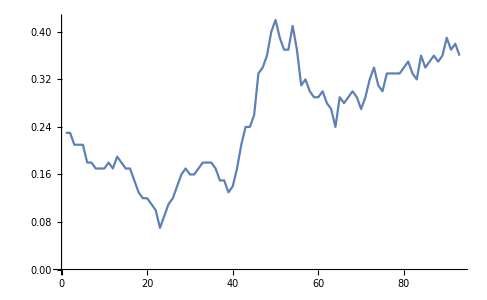

```mathematica
ListPlot[MovingAverage[BinCounts[gasTimes,{0,Max[gasTimes],10}]pulseFactor,10],Joined->True]
```

```mathematica
burntVolume=Total[BinCounts[gasTimes,{0,Max[gasTimes],10}]pulseFactor]
energyContentInBurntGas=burntVolume energyContentInGasPerCubicMeter
price=burntVolume 11 35+burntVolume 30
```

20.4

192.667

8466.

## heat

```mathematica
groundTruth={
{3786,5334},
{1585,8044},
{222,6678},
{44,1044}
};(*fűtési, hűtési*)
```

```mathematica
FormatHeatmeterEntry[entry_]:=Module[
{list},
list=StringSplit[entry,""]/.{"-"->-1};
Table[
If[list[[pos]]==-1,
Nothing,
If[
1<pos&&list[[pos-1]]==-1,
-ToExpression[list[[pos]]],
ToExpression[list[[pos]]]
]]
,{pos,1,Length[list]}]
]
```

```mathematica
startDate=DateObject["2023.11.24. 00:00"];
```

```mathematica
timeGranularity="Minute";
```

```mathematica
readout=Map[
Join[
{Round[DateDifferenceInUnits[startDate,DateObject[#[[1]]],timeGranularity],0.25]},
Map[
FormatHeatmeterEntry[#]
&,#[[2;;5]]]
]
&,Map[
StringSplit[#,","]
&,StringSplit[Import[NotebookDirectory[]<>"heatmeter_readouts.csv","Text"],"\n"]]];
```

```mathematica
heatingCumulativeUnclean=Table[DeleteDuplicates[Select[Map[
{#[[1]],ToExpression[StringRiffle[#[[2]],""]]}&,
Select[
Transpose[Transpose[readout][[{1,cycle+1}]]],
MemberQ[#[[2]],-1]==False&
]],#[[2]]-groundTruth[[cycle]][[1]]<1500&]],{cycle,1,4}];
```

```mathematica
heatingCumulativeClean=Table[Table[
If[
10<Abs[heatingCumulativeUnclean[[cycle]][[n]][[2]]-heatingCumulativeUnclean[[cycle]][[n-1]][[2]]],
Nothing,
heatingCumulativeUnclean[[cycle]][[n]]
]
,{n,2,Length[heatingCumulativeUnclean[[cycle]]]}],{cycle,1,4}];
```

```mathematica
energyContentDeliveredOnCycles=Total[Quiet[Select[Table[
Select[heatingCumulativeClean[[cycle]],0<#[[1]]&]//#[[-1]][[2]]-#[[1]][[2]]&
,{cycle,1,4}],Positive]]]
```

231

```mathematica
efficiency=100 energyContentDeliveredOnCycles/energyContentInBurntGas
```

119.896

```mathematica
heatingDiff=Table[Table[
{Mean[{heatingCumulativeClean[[cycle]][[n]][[1]],heatingCumulativeClean[[cycle]][[n-1]][[1]]}],(heatingCumulativeClean[[cycle]][[n]][[2]]-heatingCumulativeClean[[cycle]][[n-1]][[2]])/(heatingCumulativeClean[[cycle]][[n]][[1]]-heatingCumulativeClean[[cycle]][[n-1]][[1]])}
,{n,2,Length[heatingCumulativeClean[[cycle]]]}],{cycle,1,4}];
```

Power::infy: Infinite expression 1/0. encountered.

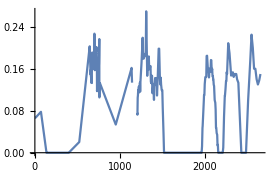
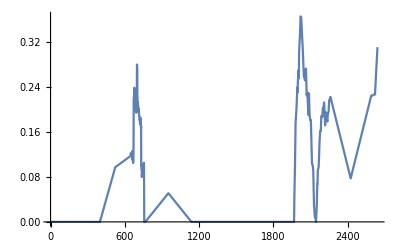
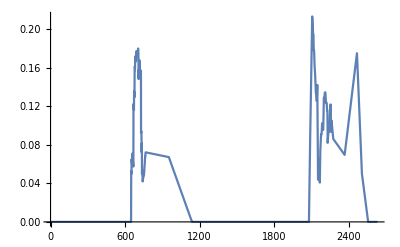
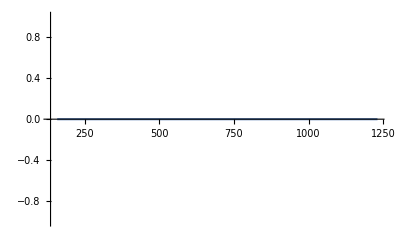

```mathematica
Table[
ListPlot[SparseTimeMovingAverage[heatingDiff[[cycle]],60 1],Joined->True,PlotRange->All]
,{cycle,1,4}]
```

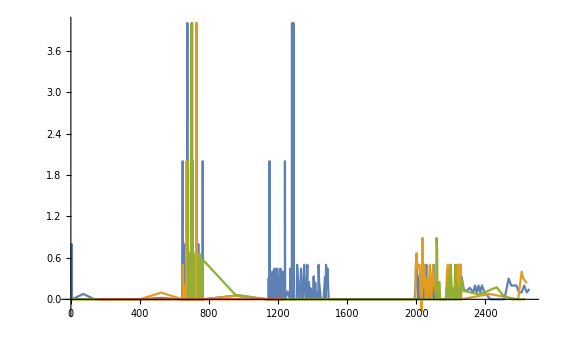

```mathematica
ListPlot[heatingDiff,Joined->True,PlotRange->All]
```